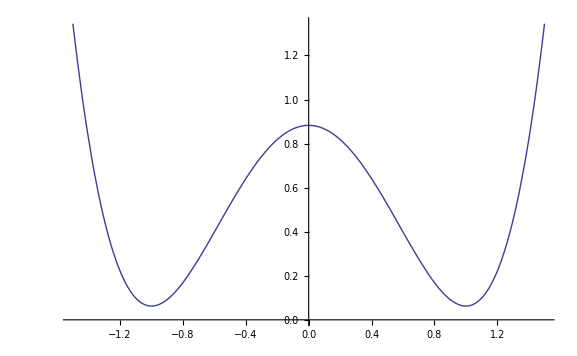

```mathematica
The graphs for exercise 6:

Plot[105/128 x^4-105/64 x^2+113/128,{x,-1.5,1.5}]
```

```mathematica
Plot[1/2+∑_(n=1)^5 4/((2n-1)^2π^2)Cos[(2n-1)π×x],{x,-1.5,1.5}]
```

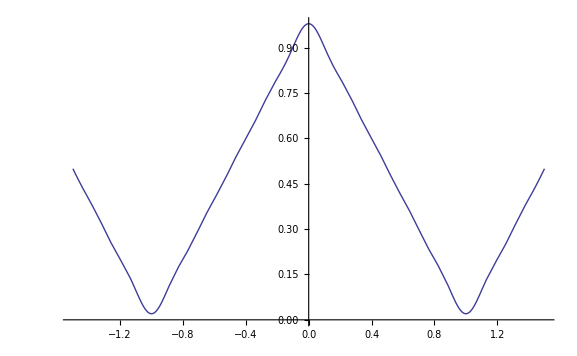
```mathematica
-Graphics-


The code for orthonomalization in exercise 6:
```

```mathematica
Orthogonalize[{1,x,x^2,x^3,x^4},Integrate[#1#2,{x,-1,1}]&]
```

```mathematica
{1/(√2),√(3/2) x,3/2 √(5/2) (-1/3+x^2),5/2 √(7/2) (-(3 x)/5+x^3),(105 (-1/5+x^4-6/7 (-1/3+x^2)))/(8 √2)}
```